```mathematica
Function CURVES GETCURVES(IMAGE)
Begin
 Curves BezierCurves;
 Pixel SignatureSegments;
 for each(pixel in Image)
 If (Color of pixel is not default color)
 SignatureSegments.Add(pixel);
End if
End for
Arrange pixels in SignatureSegments
Create new BezierCurve;
for each(pixel in SignatureSegments)
If(Change in is more than previous pixel)
 BezierCurves.Add(BezierCurve);
Create new BezierCurve;
Else
BezierCurve.Add(pixel);
End if
End for
return BezierCurves
End
```

CURVES Function GETCURVES IMAGE

Begin

each for Image in pixel

color Color default If is not of pixel

End if

End for

Arrange in pixels SignatureSegments

each for in pixel SignatureSegments

Change If in is more pixel previous than

Else

End if

End for

BezierCurves return

End

```mathematica
Matrix Form[Idenity Matrix[3]]; //MatrixForm
```

Null

```mathematica
A={{a,b},{c,d}}
MatrixForm[A]
```

{{a,b},{c,d}}

(a | b
c | d)

```mathematica
MatrixForm[IdentityMatrix[3]]//Matrix Form
```

```mathematica
(Form Matrix)[({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]
```

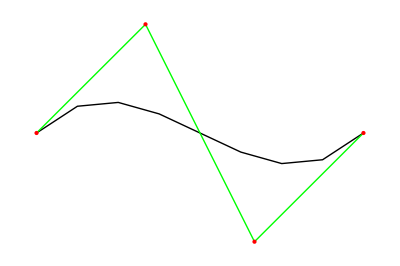

```mathematica
pts={{0,0},{1,1},{2,-1},{3,0}};
Graphics[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

BezierCurve[{{0,0},{0,2},{1,2}}]

BezierCurve[{{1,2},{2,2},{2,0}}]

BezierCurve[{{2,0},{2,-1},{1,-1}}]

BezierCurve[{{1,-1},{0,-1},{0,0}}]

BezierCurve[{{2,1},{2,-2}}]

BezierCurve[{{2,0},{2,1},{2.8,1}}]

BezierCurve[{{2.8,1},{3.5,1},{3.5,0}}]

BezierCurve[{{3.5,0},{3.5,-1},{2.8,-1}}]

BezierCurve[{{2.8,-1},{2,-1},{2,0}}]

BezierCurve[{{3.5,-1},{3.5,1}}]

BezierCurve[{{3.5,0},{3.5,1},{4.5,1}}]

BezierCurve[{{4.5,1},{5,1},{5,0.7}}]

BezierCurve[{{6.5,1},{5,1},{5,0}}]

BezierCurve[{{5,0},{5,-1},{6.5,-1}}]

BezierCurve[{{5,0},{6.5,0},{6.5,1}}]

BezierCurve[{{7,0},{7,1},{7.8,1}}]

BezierCurve[{{7.8,1},{8.6,1},{8.6,0}}]

BezierCurve[{{8.6,0},{8.6,-1},{7.8,-1}}]

BezierCurve[{{7.8,-1},{7,-1},{7,0}}]

BezierCurve[{{6.5,-1},{7,-0.7}}]

BezierCurve[{{8.6,1},{8.6,-0.8}}]

BezierCurve[{{8.6,-0.5},{8.6,-1},{9,-1}}]

BezierCurve[{{9,-1},{10,-1}}]

BezierCurve[{{10,-1},{0,-2}}]

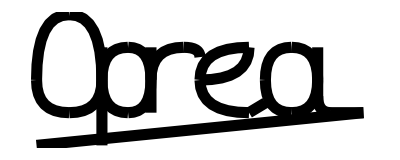

```mathematica
a=BezierCurve[{{0,0},{0,2},{1,2}}]
b=BezierCurve[{{1,2},{2,2},{2,0}}]
c=BezierCurve[{{2,0},{2,-1},{1,-1}}]
d=BezierCurve[{{1,-1},{0,-1},{0,0}}]
e=BezierCurve[{{2,1},{2,-2}}]
f=BezierCurve[{{2,0},{2,1},{2.8,1}}]
g=BezierCurve[{{2.8,1},{3.5,1},{3.5,0}}]
h=BezierCurve[{{3.5,0},{3.5,-1},{2.8,-1}}]
i=BezierCurve[{{2.8,-1},{2,-1},{2,0}}]
j=BezierCurve[{{3.5,-1},{3.5,1}}]
k=BezierCurve[{{3.5,0},{3.5,1},{4.5,1}}]
l=BezierCurve[{{4.5,1},{5,1},{5,0.7}}]
m=BezierCurve[{{6.5,1},{5,1},{5,0}}]
n=BezierCurve[{{5,0},{5,-1},{6.5,-1}}]
o=BezierCurve[{{5,0},{6.5,0},{6.5,1}}]
p=BezierCurve[{{7,0},{7,1},{7.8,1}}]
q=BezierCurve[{{7.8,1},{8.6,1},{8.6,0}}]
r=BezierCurve[{{8.6,0},{8.6,-1},{7.8,-1}}]
s=BezierCurve[{{7.8,-1},{7,-1},{7,0}}]
t=BezierCurve[{{6.5,-1},{7,-0.7}}]
u=BezierCurve[{{8.6,1},{8.6,-0.8}}]
v=BezierCurve[{{8.6,-0.5},{8.6,-1},{9,-1}}]
w=BezierCurve[{{9,-1},{10,-1}}]
x=BezierCurve[{{10,-1},{0,-2}}]
Graphics[{Black,Thickness[0.02],a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x}]
```